Last modified on: Tuesday, July 10, 2018 at 9:32

Author Info

Faizon Zaman

Matteo Salvarezza

SUNY Oswego

Poster Session Content

Wolfram-Twine Bridge

The goal is to build an Import/Export system between Twine and the Wolfram Language. Twine is browser-based software used to make interactive stories and text-based games. A Twine story or game consists of a network of passages and macros that can change the state of variables or other story elements. Graphs and Associations will be used to represent Twine Stories in the Wolfram Language. The primary goal is importing the Twine Story HTML file into the form of a Wolfram Language Graph and Association, and exporting an Association form to the Twine HTML format.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Import support for Twine Stories made using the Harlowe markup language. The importer can generate a Graph and Association from for any html file with the Twine  format. The Twine Link syntax is supported as long as it is not in a macro (commands for changing states of story elements). Using the Association form,  a Twine Summary can be generated to explore the passages via a Clickable Graph. Association Forms  can be exported to the Twine HTML format. A folder is generated in the notebook directory where the story will be stored. These can then be imported into Twine.

The Harlowe markup language has support for macros: commands that can change story elements (appearance, flow, state etc.). Among other types, there are conditional, printing, data and output macros. Some macros include Links to other passages, which I can’t support yet as they are effectively hidden from my parser.  In addition to the macros,  proper passage placement when Importing to the Twine Editor is needed. Going forward, macros should be gradually implemented and the collection of Twine Stories to Import and test on should grow . As errors or unsupported features arise while processing these stories  I will attempt implementations and fixes.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Import

-Graphics-

twineImport["~/Documents/Twine/Stories/Other Story.html"]

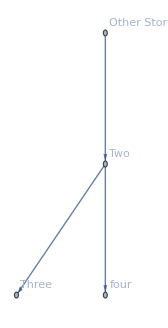

-Graphics-

Summary

twinePresentationAssoc = <|"Other Story"→<|"Two"→"Go to passage [[Three]] The other node[[four]]","Three"→"Here we are at Passage Three","four"→"Finally at Passage Four."|>|>;

twineSummary[twinePresentationAssoc]

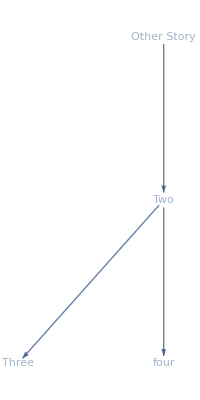

Output the graph only
twineSummary[twinePresentationAssoc, “Graph”]

Export as Twine HTML to folder called TwineStories in  current notebook directory 
twineSummary[twinePresentationAssoc, “Export”]

Export

Export as Twine HTML to specified folder
twineExport[twinePresentationAssoc, “~/Explicit/Path/For/File”]

Import to Twine

-Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

Global`content::shdw: Symbol content appears in multiple contexts {Global`,Twine`}; definitions in context Global` may shadow or be shadowed by other definitions.

#### Main Results in Detail

| IMPORTER |

Import of Twine Stories made using the Harlowe markup language. Harlowe is the default markup language for the Twine Editor  (there are two others: snowman and sugarcube).  On import, a Graph and Association form of the Twine Story are created. Links that only exist as a result of a macro are not supported yet.

| EXPORTER |

The exporter takes an Association form of a story and exports it as an HTML Fragment that can be imported into Twine. 

| SUMMARIZER |

The summarizer has three functions; Summary which returns a GraphicsRow containing the Graph with Button vertices and a simple passage display  Graph which returns the Graph with Button Vertices by itself, and Export which exports the story in HTML format to a folder called TwineStories.

#### Code

GitHub Repo

#### Notes

The initial goal of the project is to develop an import export system between the Wolfram Language and Twine. What were the implementation tasks for this project?

First : Figure out the structure of the Twine Story:
	I found that there was a particular and simple structure representing the story.
		- <tw-storydata> <tw-passagedata></tw-passaagedata> … </tw-storydata>
		The builtin parser was having troube parsing the Twine HTML file correctly, Riccardo wrote a parser that nested the elements correctly. From there I was able to pick apart the neccessary elements and generate a graph and association from the story.

Another thingI did was implement an exporter and summarizer. The summarizer takes in the association form and can show a button graph with a dynamic passage viewer that changes by button clicks, or just the graph, or just Export the file. The summarizer exports to the TwineStories folder in the Notebook Directory

The twinExport function allows one to specify directly / explicitly where to save the files via a path string.

These are the basic results. I will look through my project files and notes that I wrote and add them to the Project notebook. I started attempting implementation of macros.

Do I Need the Intermediate File—Twine saves intermediate files to the browser’s local storage, can’t access this
Exploration—Twine stories are about exploration. Do we want the Graph representation in WL to be explorable?
If yes, it won’t be like the exploration in Twine itself. It will be a computable exploration. Look at Graph functions for some insight.

–	Just focus on Harlowe markup support (which is the default markup language for Twine)

Initially, the Exported HTML did not work in Twine because I neglected the metadata of tw-storydata and tw-passagedata tags. After I hardcoded the metadata Exports worked. The question with this is how to keep the metadata up to date.

Not including metadata caused The Twine app to hang, so I had to re-download it

#### Conclusions in Detail

It is relatively easy to work with HTML. It may have been a bug that nested the tags improperly. Riccardo’s code fixed that problem so I could import the html correctly.  
I learned how to represent Twine’s particular HTML structure in Association and Graph forms. I learned how to extract and replace String Patterns. I learned how to Generate Graphs and replace their vertices with buttons.

There was a lot of Extraction from Data Structures, Replacing and Isolating String Patterns

How well did I succeed in the original goal?

I now have the framework to build a comprehensive Twine Import/Export system. I can build upon my simple import to include support for macros, and eventually user-scripts. I can build upon my simple export to include support for proper Passage Positioning for the Twine editor.

#### Data Sources Links/References

Zip File (Contains the html) | Depths of Sarcasm

#### Future Directions

If all goes well, Machine generated stories generated by the Wolfram Language can be exported as twine stories and uploaded to the internet, (or perhaps any graph). Whether the Graph in WL can be explored in a Twine-Like way via the notebook, is yet to be determined.
The Harlowe markup language has support for macros: commands that can change story elements (appearance, flow, state etc.). Among other types, there are conditional, printing, data and output macros. Some macros include Links to other passages, which I can’t support yet as they are effectively hidden from my parser. The next step is to gradually implement these macros and continually increase the number of stories I am testing on. For each parsing or macro error in a story, I can implement a fix.

Working with opensource software — this means I’m going to have to maintain this functionality as the Harlowe markup language changes

Passage Position on Export

#### Background Info Links/References

Twine Reference

Harlowe Macro Reference

Harlowe Reference

#### Keywords

Provide keywords as items

Twine

Import

Export

Narrative

Explore

Graph

Interactive